```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Dir = "/home/matt/git/git/fast-fourier-transform/fast-fourier/results";
Thread1=Import[StringJoin[Dir,"/1.txt"], "Table"];
Thread2=Import[StringJoin[Dir,"/4.txt"], "Table"];
Thread3=Import[StringJoin[Dir,"/16.txt"], "Table"];
Thread4=Import[StringJoin[Dir,"/64.txt"], "Table"];
Thread5=Import[StringJoin[Dir,"/256.txt"], "Table"];
Thread6=Import[StringJoin[Dir,"/1024.txt"], "Table"];
```

```mathematica
DS1 = Table[{{Thread1[[n]][[1]],Thread1[[n]][[2]]},  ErrorBar[ Thread1[[n]][[3]] ]},{n,1,Length[Thread1]}];
DS2 = Table[{{Thread2[[n]][[1]],Thread2[[n]][[2]]},  ErrorBar[ Thread2[[n]][[3]] ]},{n,1,Length[Thread2]}];
DS3 = Table[{{Thread3[[n]][[1]],Thread3[[n]][[2]]},  ErrorBar[ Thread3[[n]][[3]] ]},{n,1,Length[Thread3]}];
DS4 = Table[{{Thread4[[n]][[1]],Thread4[[n]][[2]]},  ErrorBar[ Thread4[[n]][[3]] ]},{n,1,Length[Thread4]}];
DS5 = Table[{{Thread5[[n]][[1]],Thread5[[n]][[2]]},  ErrorBar[ Thread5[[n]][[3]] ]},{n,1,Length[Thread5]}];
DS6 = Table[{{Thread6[[n]][[1]],Thread6[[n]][[2]]},  ErrorBar[ Thread6[[n]][[3]] ]},{n,1,Length[Thread6]}];
```

```mathematica
DA1 = Table[DS1[[n]][[1]],{n,1,Length[Thread1]}];
DA2 = Table[DS2[[n]][[1]],{n,1,Length[Thread2]}];
DA3 = Table[DS3[[n]][[1]],{n,1,Length[Thread3]}];
DA4 = Table[DS4[[n]][[1]],{n,1,Length[Thread4]}];
DA5 = Table[DS5[[n]][[1]],{n,1,Length[Thread5]}];
DA6 = Table[DS6[[n]][[1]],{n,1,Length[Thread6]}];
```

```mathematica
DA1
```

{{131072,7373.71},{524288,35790.6},{2097152,162529},{8388608,773815},{33554432,3.42766×10^6}}

```mathematica
M1=NonlinearModelFit[DA1,a x Log[x]+b x + c Log[x],{a,b,c},x];
M2=NonlinearModelFit[DA2,a x Log[x]+b x + c Log[x],{a,b,c},x];
M3=NonlinearModelFit[DA3,a x Log[x]+b x + c Log[x],{a,b,c},x];
M4=NonlinearModelFit[DA4,a x Log[x]+b x + c Log[x],{a,b,c},x];
M5=NonlinearModelFit[DA5,a x Log[x]+b x + c Log[x],{a,b,c},x];
M6=NonlinearModelFit[DA6,a x Log[x]+b x + c Log[x],{a,b,c},x];
```

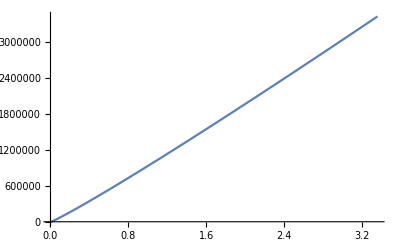

```mathematica
Plot[M1[x],{x,4096, 2^(25)+1000}]
```

```mathematica
M1[x]
```

-0.0202128 x-313.659 Log[x]+0.0070713 x Log[x]

```mathematica
Err=ErrorListPlot[{DS1,DS2,DS3,DS4,DS5,DS6}];
```

```mathematica
BF = Plot[{M1[x],M2[x],M3[x],M4[x],M5[x],M6[x]},{x,0,2^(25)+1000}, PlotLegends->{"1 Thread","4 Threads" , "16 Threads", "64 Threads", "256 Threads", "1024 Threads"}, PlotRange->{{0,2^(25)+1000},{0,4000000}}];
```

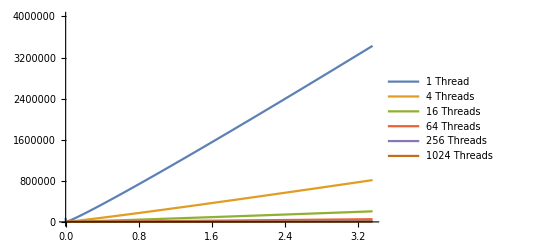

```mathematica
BF
```

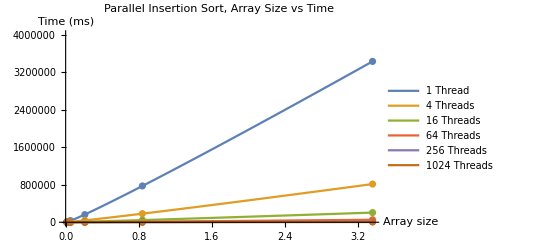

```mathematica
Show[Err,BF,AxesLabel-> {"Array size", "Time (ms)"},PlotRange->{{0,2^(25)+1000},{0,4000000}}, PlotLabel-> "Parallel Insertion Sort, Array Size vs Time"]
```

```mathematica
tab = {DA1, DA2, DA3, DA4, DA5,DA6}
```

{{{131072,7373.71},{524288,35790.6},{2097152,162529},{8388608,773815},{33554432,3.42766×10^6}},{{131072,1747.24},{524288,8465.2},{2097152,38511.3},{8388608,183374},{33554432,813669}},{{131072,445.596},{524288,2145.66},{2097152,9747.84},{8388608,46412},{33554432,205829}},{{131072,117.242},{524288,552.491},{2097152,2508.03},{8388608,11884},{33554432,52810.5}},{{131072,33.8304},{524288,148.929},{2097152,668.6},{8388608,3142.33},{33554432,14307.3}},{{131072,11.0459},{524288,46.11},{2097152,201.333},{8388608,975.441},{33554432,4653.17}}}

```mathematica
TableForm[tab]
```

131072
7373.71 | 524288
35790.6 | 2097152
162529 | 8388608
773815 | 33554432
3.42766×10^6
131072
1747.24 | 524288
8465.2 | 2097152
38511.3 | 8388608
183374 | 33554432
813669
131072
445.596 | 524288
2145.66 | 2097152
9747.84 | 8388608
46412 | 33554432
205829
131072
117.242 | 524288
552.491 | 2097152
2508.03 | 8388608
11884 | 33554432
52810.5
131072
33.8304 | 524288
148.929 | 2097152
668.6 | 8388608
3142.33 | 33554432
14307.3
131072
11.0459 | 524288
46.11 | 2097152
201.333 | 8388608
975.441 | 33554432
4653.17